# Thunderstorm Analyzer

ABSTRACT:
The goal of this project is the creation of a system which will automatically get the data from public weather servers, analyze quantities like the number of cosmic rays, levels of ionizing radiation, electrostatic field strength, etc., and study their temporal correlation to detect the cases of Thunderstorm ground enhancements (TGE).
Thunderstorm ground Enhancement is a process of increase in the level of gamma radiation, number of electrons and neutrons, connected to the propagation of cosmic rays through strong atmospheric electric fields.
It was observed that during thunderstorms electrostatic field increases by orders of magnitude and gamma radiation levels as well as number of neutrons and relativistic electrons increase up to 10 times above cosmic ray background. When electrostatic field reaches certain levels lightning happens and the level of gamma radiation, electrons and neutrons as well as the field itself fall down immediately after the lightning.
The TGE events are characterized by following 7 criteria:

Large fluxes of electrons and gamma rays with durations around 10 minutes;

Increase in neutron number;

Microsecond electron bursts with around 50ms duration;

Increase of high energy muon level;

Large, usually negative, near-surface electric field, rising sometimes from deep negative to near zero positive values. Usually field is at the level of -10 - -30 kV/m;

Decrease of the cloud-ground lightnings and increase of intra-cloud lightnings.

Increase of relative humidity above 80% and decrease of air temperature below 5-6 degrease Celsius.

The system should analyze all the data and look for this kind of events and notify us upon their occurring.

## Import Weather Data from csv file.

#### Delete corrupted sublists and the first element of the list which contains header of csv file.

#### Data importer from csv file.

```mathematica
dataImporter[filePath_String, nOfColumns_Integer]:=Select[
	DeleteCases[
		Delete[
			Import[
				StringJoin[
					NotebookDirectory[], filePath
				]
			],
			1
		],
		"", {2}
	],
	(Length[#] == nOfColumns)&
];
```

#### Conversion rule for converting month names to month numbers.

```mathematica
monthRule:={"Jan"->1,"Feb"->2,"Mar"->3,"Apr"->4,"May"->5,"Jun"->6,"Jul"->7,"Aug"->8,"Sep"->9,"Oct"->10,"Nov"->11,"Dec"->12};
```

#### Transforms the date to the format of {y, m, d, h, m, s}

```mathematica
dateFormater[inputList_] := Replace[
	Part[
		MapAt[
			ToExpression,
			ReplaceAll[
				StringSplit[
					inputList,
					":" | " " | "-"
				],
				monthRule],
			{All,{1,2,3,4,5,6}}
		],All, {3, 2, 1, 4, 5, 6}
	],
	{year_, rest__} :> {year+2000, rest},
	{1}
];
```

### Import Electric Filed Data

```mathematica
electricFieldFull = dataImporter["Weather Data (05.Jul - 07.Jul.16)\\Electric_Field_MAKET.csv", 2];

electricFieldFullConverted = Transpose[{dateFormater[electricFieldFull[[All,1]]], electricFieldFull[[All,2]]}];
```

```mathematica
electricField = Part[
	electricFieldFullConverted,
	Position[
		electricFieldFullConverted,
		{2016, 7, 6, 06, 00, 00.}][[1, 1]] ;; Position[electricFieldFullConverted, {2016, 7, 6, 14, 00, 00.}][[1, 1]]
];
```

### Import STAND Electron and Gamma ray Detector Data

```mathematica
stand1Raw = dataImporter["Weather Data (05.Jul - 07.Jul.16)\\Stand_1cm.csv", 13];

stand1 = Transpose[{dateFormater[stand1Raw[[All,1]]],stand1Raw[[All,2]]}];
stand1Normalized = Transpose[{dateFormater[stand1Raw[[All,1]]],N[Rescale[stand1Raw[[All,2]],{Min[stand1],Max[stand1]},{0, 20}]]}];
```

### Import NaI Electron and Gamma ray Detector Data

```mathematica
naIFull = dataImporter["Weather Data (05.Jul - 07.Jul.16)\\NaI.csv",19];
naIFull = naIFull[[4;;]];

naI3 = Transpose[
	{dateFormater[naIFull[[All, 1]]], naIFull[[All, 3]]}
];

naI3Normalized = Transpose[{dateFormater[naIFull[[All,1]]],N[Rescale[naIFull[[All,2]],{Min[naI3],Max[naI3]},{0, 20}]]}];
```

### Import temperature and humidity data.

```mathematica
weatherData = Select[
	Delete[
		Import[
			StringJoin[NotebookDirectory[],"Weather Data (05.Jul - 07.Jul.16)\\Weather_Station.csv"]
		],
		1
	],
	(Length[#] == 37)&
];

weatherDataOrder = {
	{1,"Date/Time"},{2,"Outside Temperature"},{3,"Hi Temperature"},{4,"Low Temperature"},{5,"Outside Humidity"},
	{6,"Dew Point"},{7,"Wind Speed"},{8,"Wind Direction"},{9,"Wind Run"},{10,"Hi Wind Speed"},{11,"Hi Wind Direction"},
	{12,"Wind Chill"},{13,"Heat Index"},{14,"THW Index"},{15,"THWS Index"},{16,"Pressure"},{17,"Rain"},
	{18,"Rain Rate"},{19,"Solar Radiation"},{20,"Solra Energy"},{21,"Hi Solar Radiation"},{22,"UV Index"},{23,"UV Dose"},
	{24,"Hi UV"},{25,"Heating D-D"},{26,"Cooling D-D"},{27,"Inside Temperature"},{28,"Inside Humidity"},{29,"Inside Dew Point"},
	{30,"Inside Heat"},{31,"Inside EMC"},{32,"Inside Air Density"},{33,"ET"},{34,"Wind Samp"},{35,"Wind TX"},{36,"ISS Recept"},{37,"Arc Int\n"}
};

temperature = Transpose[{dateFormater[weatherData[[All, 1]]], weatherData[[All, 2]]}];
humidity = Transpose[{dateFormater[weatherData[[All, 1]]], weatherData[[All, 5]]}];
```

#### Generate the plot of electric field

```mathematica
(*eFieldplottingRange = {{{2016,8,1,11,00,00},{2016,8,1,12,00,00}},{-20,20}};*)
(*eFieldplottingRange = {{{2016,8,1,11,30,00},{2016,8,1,11,45,00}},{-20,20}};*)
eFieldPlottingRange = Full;
naI3PlottingRange = Full;
plottingRange = {{{2016,7,6,12,00,00},{2016,7,6,23,00,00}},{47000,68000}};
```

```mathematica
plotOriginal[data_, rangeMin_, rangeMax_, rangeStep_] := DateListPlot[
	data,
	Filling->Axis,
	PlotRange->plottingRange,
	Joined->False,
	PlotTheme->"Detailed",
	FrameTicks->{{Range[rangeMin, rangeMax, rangeStep],None},All}
]
```

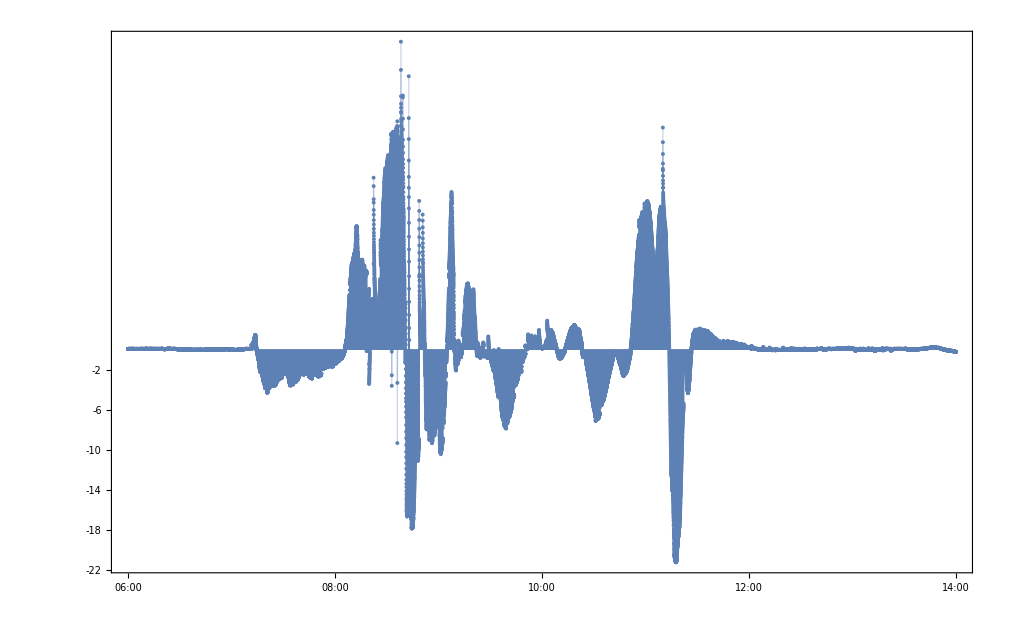

```mathematica
plotEField=plotOriginal[electricField,-50,50, 1]
```

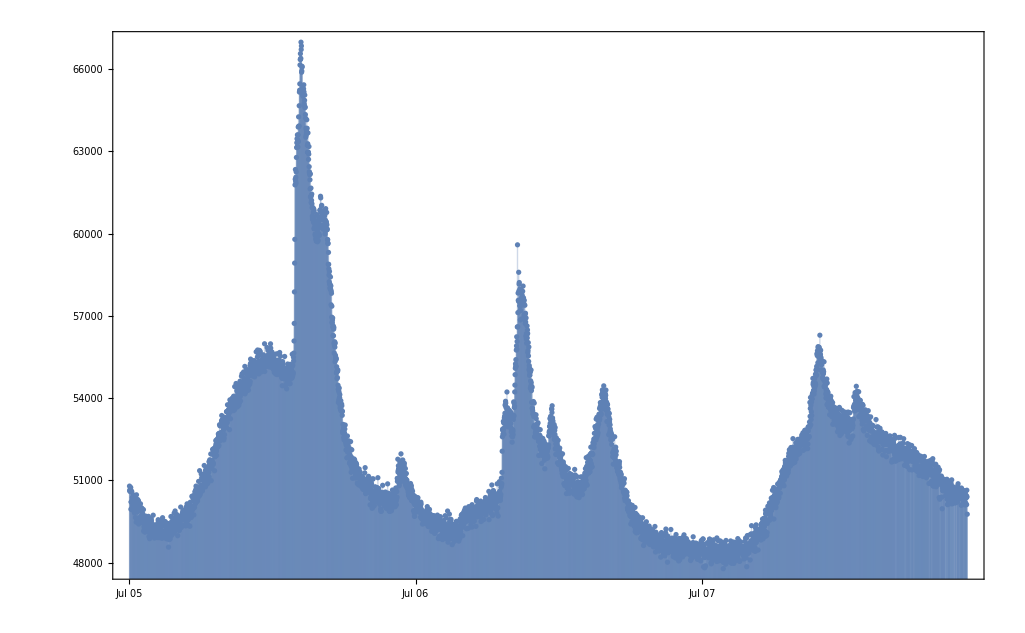

```mathematica
plotNaI3 = DateListPlot[
	naI3,
	Filling->Axis,
	PlotRange->naI3PlottingRange,
	Joined->False,
	PlotTheme->"Detailed",
	FrameTicks->{{Range[30000, 70000, 1000],None},All}
]
```

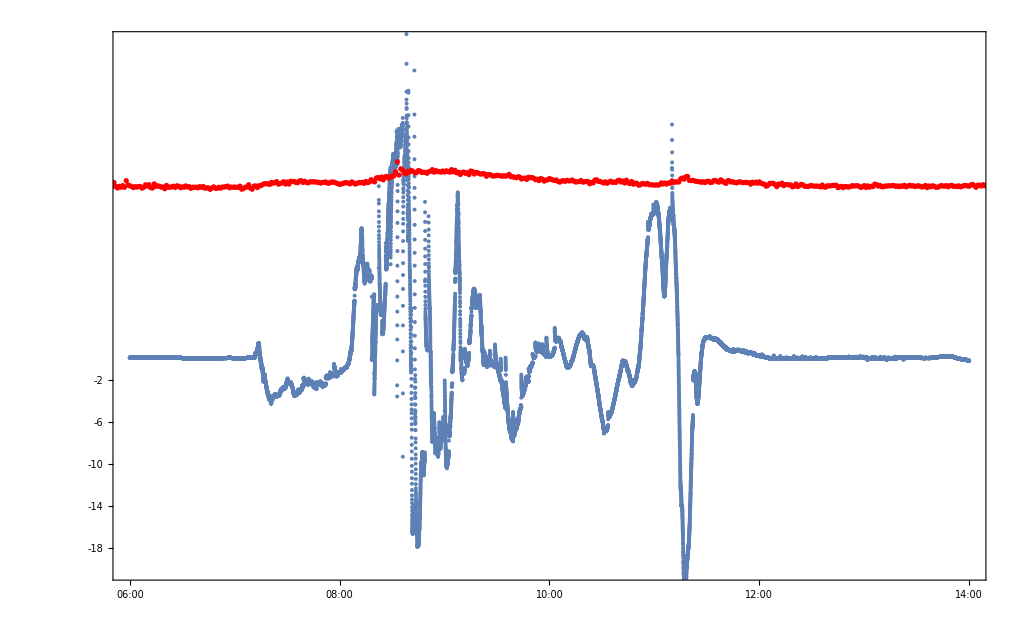

```mathematica
Show[DateListPlot[electricField,PlotRange->{-20,30},Joined->False,PlotTheme->"Detailed",
	FrameTicks->{{Range[-50,50,1],None},All}],DateListPlot[stand1Normalized,PlotRange->Full,PlotStyle->Red,Joined->False]]
```

#### Get local minima and maxima in time series and apply a low cut filters

```mathematica
getMaxs[detectorData_, sigma_, sharpness_, triggerShreshold_] := DeleteCases[
	Pick[
		detectorData,
		PeakDetect[
			detectorData[[All, 2]],
			sigma,
			sharpness
		],
		1
	],
	{date_,data_}/;data ≥ triggerShreshold
];
getMaxs[detectorData_, sigma_, sharpness_] := Pick[
	detectorData,
	PeakDetect[
		detectorData[[All, 2]],
		sigma,
		sharpness
	],
	1
];

getMins[detectorData_, sigma_, sharpness_, triggerShreshold_] := DeleteCases[
	Pick[
		detectorData,
		PeakDetect[
			-detectorData[[All, 2]],
			sigma,
			sharpness
		],
		1
	],
	{date_,data_}/;data ≥ triggerShreshold
];
getMins[detectorData_, sigma_, sharpness_] := Pick[
	detectorData,
	PeakDetect[
		-detectorData[[All, 2]],
		sigma,
		sharpness
	],
	1
];
```

```mathematica
eFieldMins=getMins[electricField, 30, 0, -7];
eFieldMaxs=getMaxs[electricField, 50, 0, -0.5];
```

```mathematica
naI3Mins = getMins[naI3, 50, 0.3];
naI3Maxs = getMaxs[naI3,15, 1.3];
```

#### Construct a graph of a data with minimas and maximas.

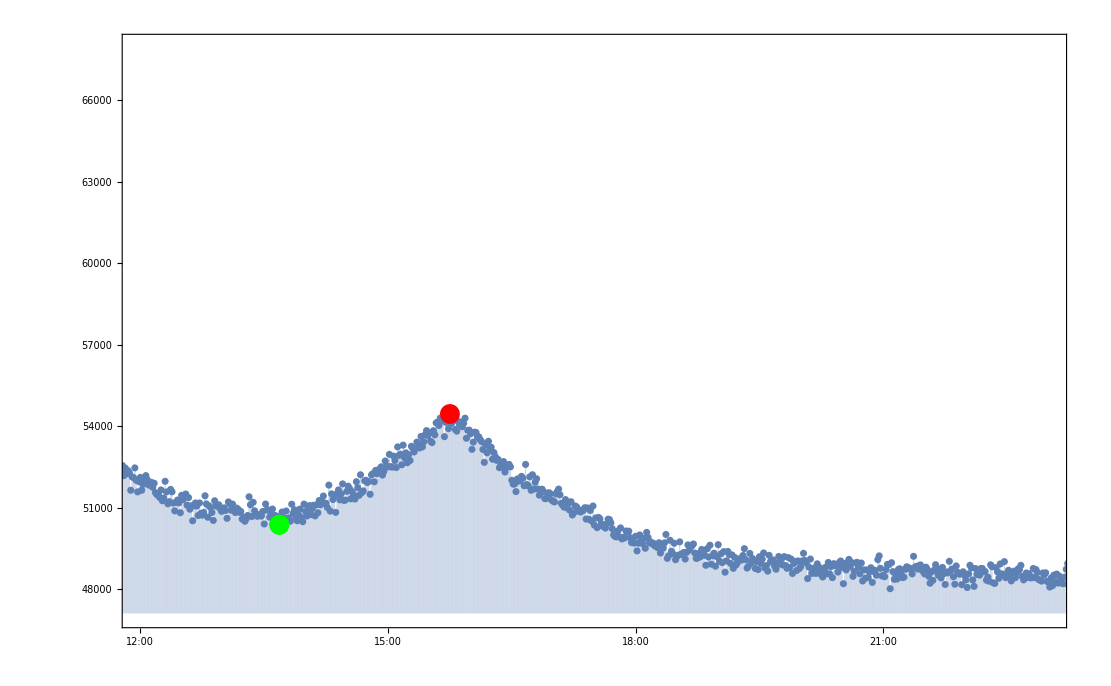

```mathematica
Show[
 	plotNaI3,
 	DateListPlot[
  		naI3Maxs,
  		PlotStyle -> Red,
  		PlotRange -> naI3PlottingRange,
  		Joined -> False
  	],
 	DateListPlot[
  		naI3Mins,
  		PlotStyle -> Green,
  		PlotRange -> naI3PlottingRange,
  		Joined -> False
  	]
 ]
```

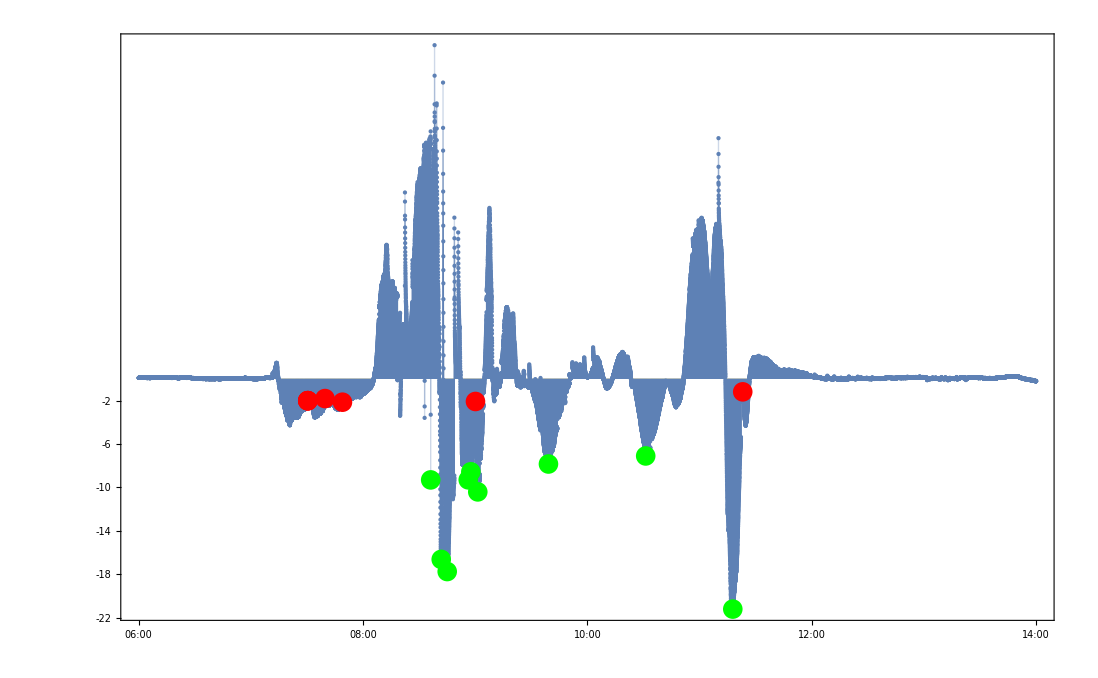

```mathematica
Show[
	plotEField,
	DateListPlot[
		eFieldMaxs,
		PlotStyle->Red,
		PlotRange->eFieldPlottingRange,
		Joined->False
	],
	DateListPlot[
		eFieldMins,
		PlotStyle->Green,
		PlotRange->eFieldPlottingRange,
		Joined->False
	]
]
```

## Find the start and end of the peaks

```mathematica
eFieldplottingRange = {{{2016,8,1,11,00,00},{2016,8,1,12,00,00}},{-20,20}};
```

```mathematica
naIplottingRange = {{{2016,8,1,11,30,00},{2016,8,1,11,45,00}},{-20,20}};
```

```mathematica
eFieldPeakPositions=Flatten[Position[electricField, #]&/@eFieldMins];
naI3PeakPositions=Flatten[Position[naI3, #]&/@naI3Maxs];
```

```mathematica
(* Example of Function usage: moveToRight[electricField, eFieldPeakPosition, 2, 1200] *)
moveToRight[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_Integer, triggerThreshold_] := Select[
	Transpose[{
		Range[1, windowSize+1, windowStep],
		TimeSeriesAggregate[
			Part[
				data[[All,2]],
				Span[Part[peakPositions,peakN], Part[peakPositions,peakN]+windowSize]
			],
			windowStep
		]
	}],
	(#[[2]] ≤ triggerThreshold)&
];

moveToRight[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_Integer] := Transpose[{
	Range[1, windowSize+1, windowStep],
	TimeSeriesAggregate[
		Part[
			data[[All,2]],
			Span[Part[peakPositions,peakN], Part[peakPositions,peakN]+windowSize]
		],
		windowStep
	]
}];
```

```mathematica
(* Example of Function usage: moveToLeft[electricField, eFieldPeakPosition, 2, 1200] *)
moveToLeft[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_Integer, triggerThreshold_] := Select[
	Transpose[{
		Range[-windowSize-1, -1, windowStep],
		TimeSeriesAggregate[
			Part[
				data[[All,2]],
				Span[Part[peakPositions, peakN]-windowSize, Part[peakPositions, peakN]]
			],
			windowStep
		]
	}],
	(#[[2]] ≤ triggerThreshold)&
];

moveToLeft[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_Integer] := Transpose[{
	Range[-windowSize-1, -1, windowStep],
	TimeSeriesAggregate[
		Part[
			data[[All,2]],
			Span[Part[peakPositions, peakN]-windowSize, Part[peakPositions, peakN]]
		],
		windowStep
	]
}];
```

```mathematica
rightEdge[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_Integer, triggerThreshold_] := Part[
	data,
	(Part[
		Select[
			moveToRight[data, peakPositions, peakN, windowSize, windowStep],
			#[[2]]==Min[moveToRight[data, peakPositions, peakN, windowSize, windowStep, triggerThreshold][[All,2]]]&
		],
		1,
		1
	] + peakPositions[[peakN]])
];

rightEdge[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_Integer] := Part[
	data,
	(Part[
		Select[
			moveToRight[data, peakPositions, peakN, windowSize, windowStep],
			#[[2]]==Min[moveToRight[data, peakPositions, peakN, windowSize, windowStep][[All,2]]]&
		],
		1,
		1
	] + peakPositions[[peakN]])
];
```

```mathematica
leftEdge[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_, triggerThreshold_] := Part[
	data,
	(Part[
		Select[
			moveToLeft[data, peakPositions, peakN, windowSize, windowStep],
			#[[2]]==Min[moveToLeft[data, peakPositions, peakN, windowSize, windowStep, triggerThreshold][[All,2]]]&
		],
		1,
		1
	] + peakPositions[[peakN]])
];

leftEdge[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_] := Part[
	data,
	(Part[
		Select[
			moveToLeft[data, peakPositions, peakN, windowSize, windowStep],
			#[[2]]==Min[moveToLeft[data, peakPositions, peakN, windowSize, windowStep][[All,2]]]&
		],
		1,
		1
	] + peakPositions[[peakN]])
];
```

```mathematica
eFieldRightEdges=(rightEdge[electricField,eFieldPeakPositions,#,1200, 30, 0])&/@Range[1,Length[eFieldPeakPositions]];
eFieldLeftEdges=(leftEdge[electricField,eFieldPeakPositions,#,1200, 30, 0])&/@Range[1,Length[eFieldPeakPositions]];
```

```mathematica
naI3RightEdges=(rightEdge[naI3,naI3PeakPositions,#,21, 1])&/@Range[1,Length[naI3PeakPositions]];
naI3LeftEdges=(leftEdge[naI3,naI3PeakPositions,#,21, 1])&/@Range[1,Length[naI3PeakPositions]];
```

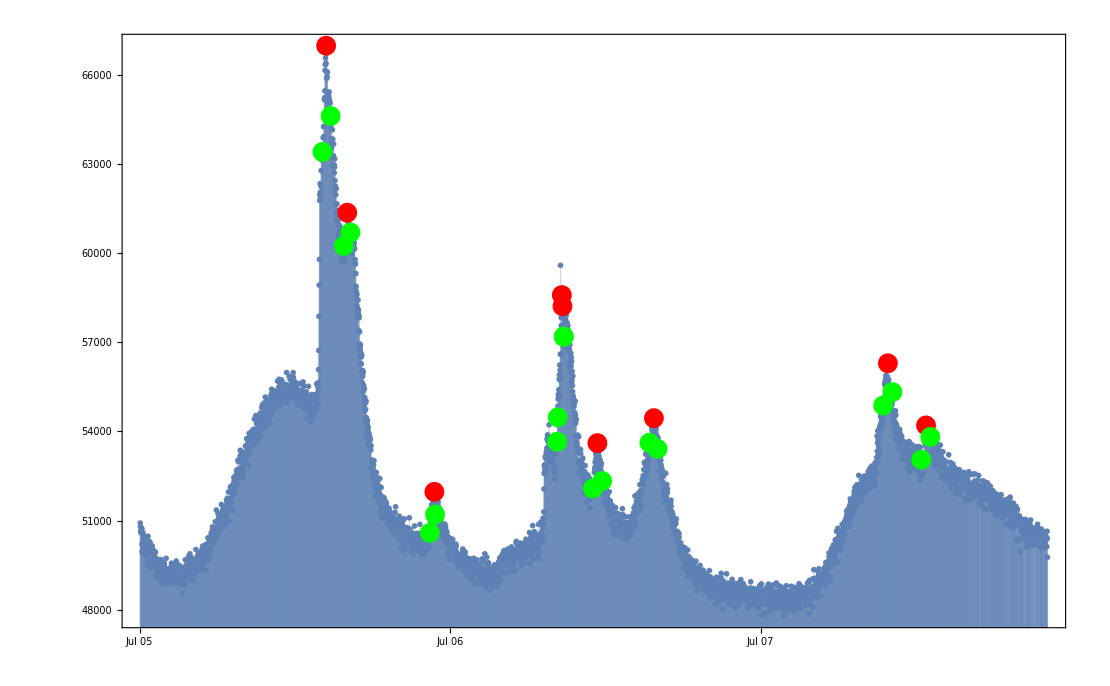

```mathematica
Show[
 	plotNaI3,
 	DateListPlot[
  		naI3Maxs,
  		PlotStyle -> Red,
  		PlotRange -> naI3PlottingRange,
  		Joined -> False
  	],
  	DateListPlot[
  		naI3LeftEdges,
  		PlotStyle -> Green,
  		PlotRange -> naI3PlottingRange,
  		Joined -> False
  	],
  	DateListPlot[
  		naI3RightEdges,
  		PlotStyle -> Green,
  		PlotRange -> naI3PlottingRange,
  		Joined -> False
  	]
 ]
```

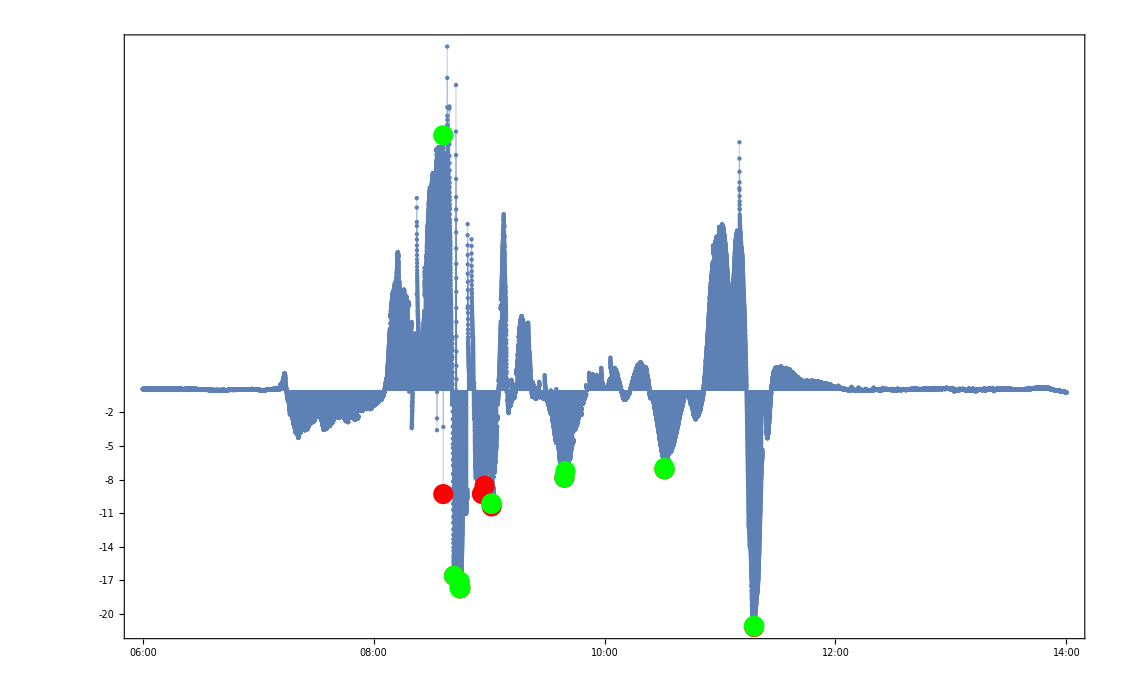

```mathematica
Show[
	plotEField,
	DateListPlot[
		eFieldMins,
		PlotStyle->Red,
		PlotRange->eFieldPlottingRange,
		Joined->False
	],
	DateListPlot[
		eFieldLeftEdges,
		PlotStyle->Green,
		PlotRange->eFieldPlottingRange,
		Joined->False
	],
	DateListPlot[
		eFieldRightEdges,
		PlotStyle->Green,
		PlotRange->eFieldPlottingRange,
		Joined->False
	]
]
```

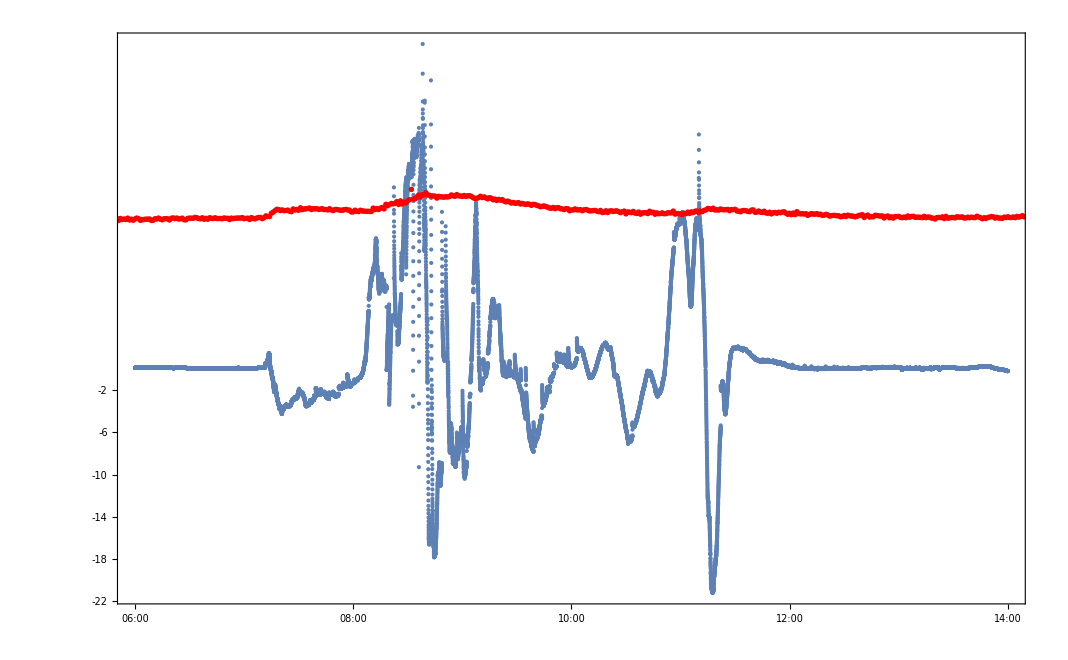

```mathematica
Show[DateListPlot[electricField,PlotRange->Full,Joined->False,PlotTheme->"Detailed",
	FrameTicks->{{Range[-50,50,1],None},All}],DateListPlot[naI3Normalized,PlotRange->Full,PlotStyle->Red,Joined->False]]
```